```mathematica
(*1.Генерация значений случайной величины методом обратных функций*)
b1=3; b2=5; b3=3; 
c1=2; c2=2; c3=3;
Clear[N0,a,b,i,Y1,X1,X2,X3];
N0=10000;
a = 0; b=1;
Y1=RandomReal[b,N0];
X1={};X2 ={}; X3={};
For[i=1,i≤N0,i++,AppendTo[X1,-c1*Surd[Log[1-Part[Y1,i]],b1]]];
For[i=1,i≤N0,i++,AppendTo[X2,-c2*Surd[Log[1-Part[Y1,i]],b2]]];
For[i=1,i≤N0,i++,AppendTo[X3,-c3*Surd[Log[1-Part[Y1,i]],b3]]];
X1=Sort[X1];
X2=Sort[X2];
X3=Sort[X3];
(*Генерация случайной величины времени отказа*)
h=0.1; (*Если брать 0.5, то получается совсем мало значений*)
Tmax1=Round[Max[X1]/h];
Tmax2=Round[Max[X2]/h];
Tmax3=Round[Max[X3]/h];
T1={};T2 ={}; T3={};
For[i=1,i≤Tmax1,i++,AppendTo[T1,i*h]];
For[i=1,i≤Tmax2,i++,AppendTo[T2,i*h]];
For[i=1,i≤Tmax3,i++,AppendTo[T3,i*h]];
```

```mathematica
(*2. Функция надёжности *)
N1={};N2={};N3={};
P1={};P2={};P3={};
For[k=1,k<Length[T1],k++,
i=1;
While[Part[T1,k]>Part[X1,i],i++];AppendTo[N1,(N0-i+1)];
AppendTo[P1,(N0-i+1)/N0]];
For[k=1,k<Length[T2],k++,
i=1;
While[Part[T2,k]>Part[X2,i],i++];AppendTo[N2,(N0-i+1)];
AppendTo[P2,(N0-i+1)/N0]];
For[k=1,k<Length[T3],k++,
i=1;
While[Part[T3,k]>Part[X3,i],i++];AppendTo[N3,(N0-i+1)];
AppendTo[P3,(N0-i+1)/N0]];
```

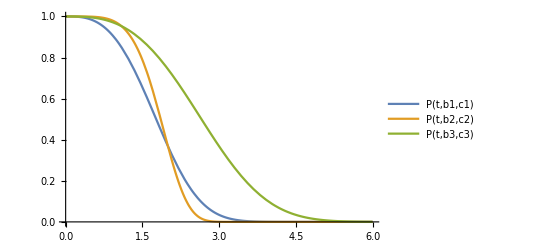

```mathematica
Clear[P,t,b,c];
P[t_,b_,c_] := E^(-(t/c)^b);
Plot[{P[t,b1,c1],P[t,b2,c2],P[t,b3,c3]},{t,0,6},PlotLegends->"Expressions"]
```

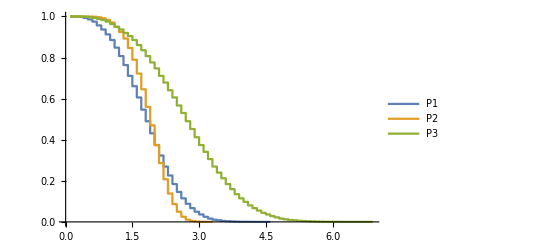

```mathematica
Matr1={}; Matr2={}; Matr3={};
For[i=1,i≤Length[P1],i++,AppendTo[Matr1,{Part[T1,i],Part[P1,i]}]];
For[i=1,i≤Length[P2],i++,AppendTo[Matr2,{Part[T2,i],Part[P2,i]}]];
For[i=1,i≤Length[P3],i++,AppendTo[Matr3,{Part[T3,i],Part[P3,i]}]];
ListStepPlot[{Legended[Matr1,"P1"],Legended[Matr2,"P2"],Legended[Matr3,"P3"]}]
```

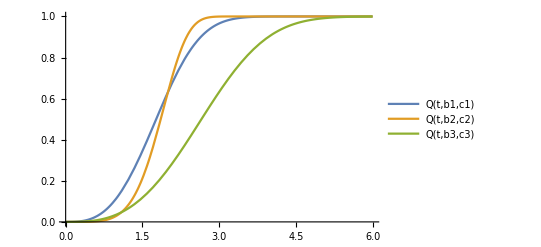

```mathematica
(*3. Функция ненадёжности *)
Q1={};Q2={};Q3={};
For[i=1,i<Length[T1],i++,AppendTo[Q1,(N0-Part[N1,i])/N0]];For[i=1,i<Length[T2],i++,AppendTo[Q2,(N0-Part[N2,i])/N0]];
For[i=1,i<Length[T3],i++,AppendTo[Q3,(N0-Part[N3,i])/N0]];
Clear[Q,t,b,c];
Q[t_,b_,c_] := 1-E^(-(t/c)^b);
Plot[{Q[t,b1,c1],Q[t,b2,c2],Q[t,b3,c3]},{t,0,6},PlotLegends->"Expressions"]
```

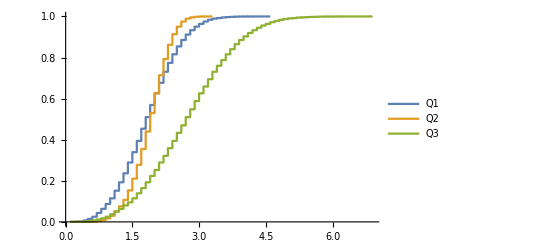

```mathematica
Matr1={}; Matr2={}; Matr3={};
For[i=1,i≤Length[Q1],i++,AppendTo[Matr1,{Part[T1,i],Part[Q1,i]}]];
For[i=1,i≤Length[Q2],i++,AppendTo[Matr2,{Part[T2,i],Part[Q2,i]}]];
For[i=1,i≤Length[Q3],i++,AppendTo[Matr3,{Part[T3,i],Part[Q3,i]}]];
ListStepPlot[{Legended[Matr1,"Q1"],Legended[Matr2,"Q2"],Legended[Matr3,"Q3"]}]
```

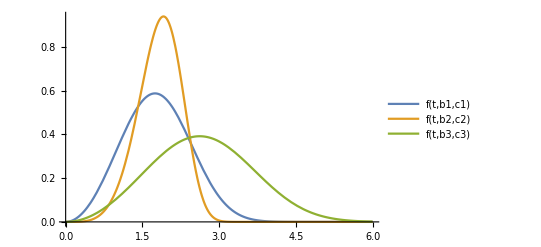

```mathematica
(*4. Функция частоты *)
f1={};f2={};f3={};
N11={};N21={};N31={};
For[k=1,k≤ Length[T1]-2,k++,
i=1;
While[(Part[T1,k]+h)>Part[X1,i],i++];AppendTo[N11,(N0-i+1)]];
For[k=1,k≤Length[T2]-2,k++,
i=1;
While[(Part[T2,k]+h)>Part[X2,i],i++];AppendTo[N21,(N0-i+1)]];
For[k=1,k≤Length[T3]-2,k++,
i=1;
While[(Part[T3,k]+h)>Part[X3,i],i++];AppendTo[N31,(N0-i+1)]];For[i=1,i<Tmax1-1,i++,AppendTo[f1,(Part[N1,i]-Part[N11,i])/(N0*h)]];
For[i=1,i<Tmax2-1,i++,AppendTo[f2,(Part[N2,i]-Part[N21,i])/(N0*h)]];
For[i=1,i<Tmax3-1,i++,AppendTo[f3,(Part[N3,i]-Part[N31,i])/(N0*h)]];

f[t_,b_,c_] := b/c(t/c)^(b-1)*E^(-(t/c)^b);
Plot[{f[t,b1,c1],f[t,b2,c2],f[t,b3,c3]},{t,0,6},PlotLegends->"Expressions"]
```

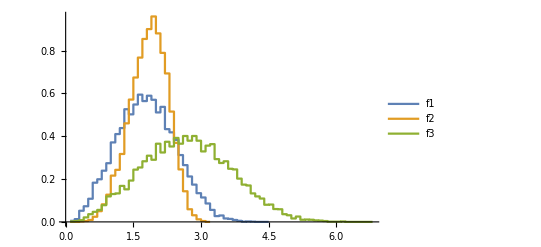

```mathematica
Matr1={}; Matr2={}; Matr3={};
For[i=1,i≤Length[f1],i++,AppendTo[Matr1,{Part[T1,i],Part[f1,i]}]];
For[i=1,i≤Length[f2],i++,AppendTo[Matr2,{Part[T2,i],Part[f2,i]}]];
For[i=1,i≤Length[f3],i++,AppendTo[Matr3,{Part[T3,i],Part[f3,i]}]];
ListStepPlot[{Legended[Matr1,"f1"],Legended[Matr2,"f2"],Legended[Matr3,"f3"]}]
```

```mathematica
(*5. Функция интенсивности *)
λ1={};λ2={};λ3={};
For[i=1,i<Tmax1-1,i++,AppendTo[λ1,(Part[N1,i]-Part[N11,i])/(Part[N1,i]*h)]];
For[i=1,i<Tmax2-1,i++,AppendTo[λ2,(Part[N2,i]-Part[N21,i])/(Part[N2,i]*h)]];
For[i=1,i<Tmax3-1,i++,AppendTo[λ3,(Part[N3,i]-Part[N31,i])/(Part[N3,i]*h)]];
```

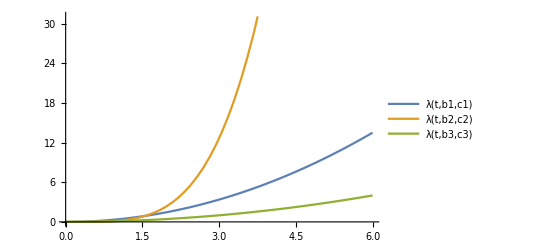

```mathematica
λ[t_,b_,c_] := f[t,b,c]/P[t,b,c];
Plot[{λ[t,b1,c1],λ[t,b2,c2],λ[t,b3,c3]},{t,0,6},PlotLegends->"Expressions"]
```

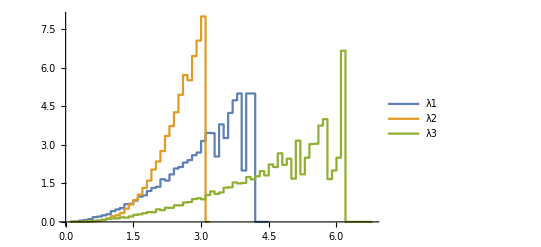

```mathematica
Matr1={}; Matr2={}; Matr3={};
For[i=1,i≤Length[λ1],i++,AppendTo[Matr1,{Part[T1,i],Part[λ1,i]}]];
For[i=1,i≤Length[λ2],i++,AppendTo[Matr2,{Part[T2,i],Part[λ2,i]}]];
For[i=1,i≤Length[λ3],i++,AppendTo[Matr3,{Part[T3,i],Part[λ3,i]}]];
ListStepPlot[{Legended[Matr1,"λ1"],Legended[Matr2,"λ2"],Legended[Matr3,"λ3"]}]
```